Project root: /Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits

Tables path:  /Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/tables

Figures path: /Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs

Logs path:    /Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/logs

<|theta0→0.7,cos_theta0→0.764842,exact_connection_Aphi→{{0.,-0.764842},{0.764842,0.}},reference_unitarity_error→5.88785×10^-17,reference_eigenphases→{-1.47754,1.47754},reference_wilson_traces_r1_r2_r3→{0.186242,-1.96531,-0.552267}|>

<|test_closure_error→3.08357×10^-16,test_max_frame_orthonormality_error→3.23683×10^-16,test_min_overlap_singular_value→0.979688|>

N | frobenius_error_to_exact_reference | unitarity_error | min_singular_value | max_projector_step_distance | max_frame_orthonormality_error | frame_closure_error | eigenphases | wilson_traces_r1_r2_r3
10 | 0.0932001 | 5.41753×10^-15 | 0.920739 | 0.551797 | 3.23683×10^-16 | 3.08357×10^-16 | {-1.41163,1.41163} | {0.316999,-1.89951,-0.919141}
20 | 0.0232254 | 1.11852×10^-14 | 0.979688 | 0.283592 | 3.23683×10^-16 | 3.08357×10^-16 | {-1.46112,1.46112} | {0.218919,-1.95207,-0.646265}
40 | 0.00580124 | 2.85828×10^-14 | 0.99489 | 0.142779 | 3.23683×10^-16 | 3.08357×10^-16 | {-1.47344,1.47344} | {0.194409,-1.96221,-0.57588}
80 | 0.00144998 | 8.01807×10^-15 | 0.998721 | 0.0715133 | 3.23683×10^-16 | 3.08357×10^-16 | {-1.47651,1.47651} | {0.188284,-1.96455,-0.558177}
160 | 0.000362476 | 1.54309×10^-14 | 0.99968 | 0.0357721 | 3.23683×10^-16 | 3.08357×10^-16 | {-1.47728,1.47728} | {0.186753,-1.96512,-0.553744}
320 | 0.0000906176 | 5.07886×10^-14 | 0.99992 | 0.017888 | 3.23683×10^-16 | 3.08357×10^-16 | {-1.47748,1.47748} | {0.18637,-1.96527,-0.552636}
640 | 0.0000226543 | 3.44969×10^-13 | 0.99998 | 0.00894424 | 3.23683×10^-16 | 3.08357×10^-16 | {-1.47752,1.47752} | {0.186274,-1.9653,-0.552359}
1280 | 5.66358×10^-6 | 7.25621×10^-13 | 0.999995 | 0.00447215 | 3.23683×10^-16 | 3.08357×10^-16 | {-1.47754,1.47754} | {0.18625,-1.96531,-0.55229}

N | frobenius_error_to_exact_reference | unitarity_error | min_singular_value | max_projector_step_distance | max_frame_orthonormality_error | frame_closure_error
10 | 0.0932001 | 5.41753×10^-15 | 0.920739 | 0.551797 | 3.23683×10^-16 | 3.08357×10^-16
20 | 0.0232254 | 1.11852×10^-14 | 0.979688 | 0.283592 | 3.23683×10^-16 | 3.08357×10^-16
40 | 0.00580124 | 2.85828×10^-14 | 0.99489 | 0.142779 | 3.23683×10^-16 | 3.08357×10^-16
80 | 0.00144998 | 8.01807×10^-15 | 0.998721 | 0.0715133 | 3.23683×10^-16 | 3.08357×10^-16
160 | 0.000362476 | 1.54309×10^-14 | 0.99968 | 0.0357721 | 3.23683×10^-16 | 3.08357×10^-16
320 | 0.0000906176 | 5.07886×10^-14 | 0.99992 | 0.017888 | 3.23683×10^-16 | 3.08357×10^-16
640 | 0.0000226543 | 3.44969×10^-13 | 0.99998 | 0.00894424 | 3.23683×10^-16 | 3.08357×10^-16
1280 | 5.66358×10^-6 | 7.25621×10^-13 | 0.999995 | 0.00447215 | 3.23683×10^-16 | 3.08357×10^-16

<|log_log_fit_intercept→2.23157,log_log_fit_slope→-2.00065,estimated_order→2.00065|>

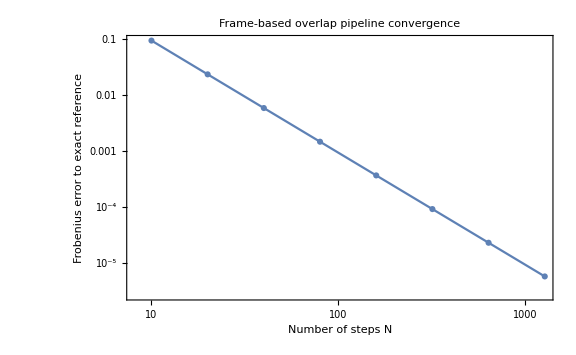

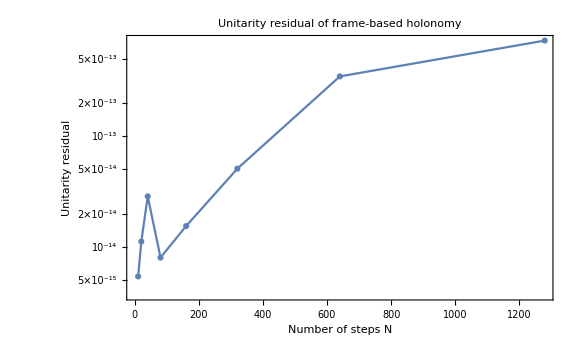

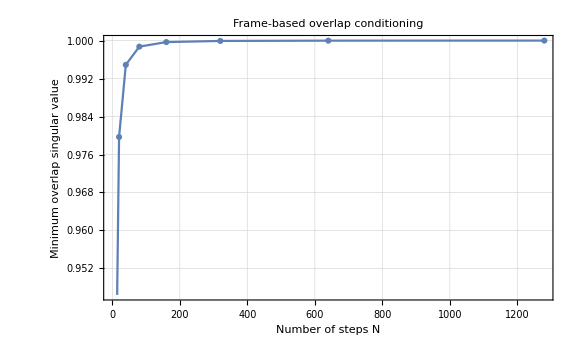

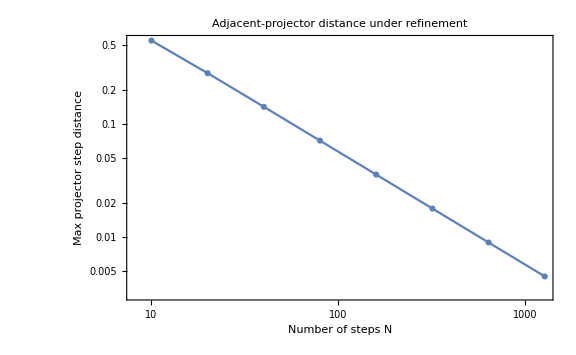

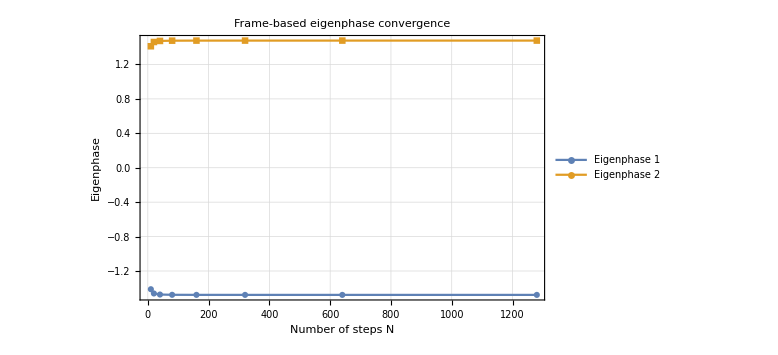

03_frame_based_overlap_pipeline.nb completed.

Purpose:
Validate the complete frame-to-overlap-to-polar-holonomy pipeline using an exact analytic frame-loop reference.

Frame path:
Rank-2 tangent frame on a sphere at fixed polar angle theta0.
theta0 = 0.7
cos(theta0) = 0.764842

Exact connection:
A_phi = {{0, -cos(theta0)}, {cos(theta0), 0}}.

Exact reference holonomy:
U_ref = Exp[-2 Pi A_phi].

Pipeline:
1. Sample frames Phi_k.
2. Construct overlaps M_k = Phi_k^dagger Phi_{k+1}.
3. Compute W_k = polar(M_k).
4. Use T_k = W_k^dagger.
5. Form Uhat = T_{N-1} ... T_0.

Expected behavior:
Frobenius error to the exact reference should decrease under mesh refinement.
Unitarity residual should remain near machine precision.
Minimum singular value should remain bounded away from zero.
Max projector step distance should decrease under refinement.

Log-log fit:
slope = -2.00065
estimated order = 2.00065

Reference diagnostics:
<|"theta0" -> 0.7, "cos_theta0" -> 0.7648421872844885, "exact_connection_Aphi" -> {{0., -0.7648421872844885}, {0.7648421872844885, 0.}}, "reference_unitarity_error" -> 5.887846720064157*^-17, "reference_eigenphases" -> {-1.4775401137225905, 1.4775401137225905}, "reference_wilson_traces_r1_r2_r3" -> {0.18624220257686608, -1.9653138419793177, -0.5522665812618972}|>

Sanity check:
<|"test_closure_error" -> 3.0835658686920554*^-16, "test_max_frame_orthonormality_error" -> 3.236828524569469*^-16, "test_min_overlap_singular_value" -> 0.9796876501920252|>

Generated files:
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/tables/03_frame_based_overlap_pipeline.csv
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/tables/03_frame_based_overlap_pipeline_numeric.csv
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/tables/03_frame_based_eigenphase_convergence.csv
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/03_frame_based_overlap_convergence.pdf
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/03_frame_based_overlap_convergence.png
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/03_frame_based_unitarity.pdf
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/03_frame_based_unitarity.png
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/03_frame_based_conditioning.pdf
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/03_frame_based_conditioning.png
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/03_frame_based_projector_step_distance.pdf
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/03_frame_based_projector_step_distance.png
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/03_frame_based_eigenphase_convergence.pdf
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/03_frame_based_eigenphase_convergence.png

Project root:
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits

<|theta0→0.7,cos_theta0→0.764842,reference_unitarity_error→5.88785×10^-17,reference_eigenphases→{-1.47754,1.47754},initial_frame_pipeline_error→0.0932001,final_frame_pipeline_error→5.66358×10^-6,max_discrete_unitarity_error→7.25621×10^-13,min_singular_value_over_all_runs→0.920739,max_initial_projector_step_distance→0.551797,max_final_projector_step_distance→0.00447215,estimated_order→2.00065,full_csv→/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/tables/03_frame_based_overlap_pipeline.csv,numeric_csv→/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/tables/03_frame_based_overlap_pipeline_numeric.csv,phase_csv→/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/tables/03_frame_based_eigenphase_convergence.csv,convergence_plot_pdf→/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/03_frame_based_overlap_convergence.pdf,unitarity_plot_pdf→/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/03_frame_based_unitarity.pdf,conditioning_plot_pdf→/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/03_frame_based_conditioning.pdf,projector_plot_pdf→/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/03_frame_based_projector_step_distance.pdf,phase_plot_pdf→/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/03_frame_based_eigenphase_convergence.pdf,log→/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/logs/03_frame_based_overlap_pipeline_log.txt|>

```mathematica
(*03—Frame-Based Overlap Pipeline Validation*)

(*This notebook validates the full frame-to-overlap-to-holonomy pipeline using an explicit rank-2 frame path with a known analytic holonomy.The frame is the tangent-frame loop on a sphere at fixed polar angle.This avoids fine-reference products and gives a direct exact reference for the polar-overlap estimator.*)

(*Initialization*)
ClearAll["Global`*"];

rootPath=ParentDirectory[NotebookDirectory[]];

SetDirectory[rootPath];
Get[FileNameJoin[{rootPath,"src","HolonomyTools.wl"}]];

(*HolonomyTools.wl clears Global`*,so re-define paths after loading.*)
rootPath=ParentDirectory[NotebookDirectory[]];
SetDirectory[rootPath];

resultsPath=FileNameJoin[{rootPath,"results"}];
tablesPath=FileNameJoin[{rootPath,"results","tables"}];
figsPath=FileNameJoin[{rootPath,"results","figs"}];
logsPath=FileNameJoin[{rootPath,"results","logs"}];

Do[If[!DirectoryQ[dir],CreateDirectory[dir,CreateIntermediateDirectories->True]],{dir,{resultsPath,tablesPath,figsPath,logsPath}}];

ClearAll[localExportCSV,localExportTXT,localExportFIG];

localExportCSV[name_String,data_]:=Module[{path},path=FileNameJoin[{tablesPath,name}];
Export[path,data,"CSV"];
path];

localExportTXT[name_String,text_String]:=Module[{path},path=FileNameJoin[{logsPath,name}];
Export[path,text,"Text"];
path];

localExportFIG[name_String,fig_]:=Module[{path},path=FileNameJoin[{figsPath,name}];
Export[path,fig];
path];

SeedRandom[34567];

Print["Project root: ",rootPath];
Print["Tables path:  ",tablesPath];
Print["Figures path: ",figsPath];
Print["Logs path:    ",logsPath];

(*Local safe product implementation*)

ClearAll[safeProduct,localForwardStepsFromOverlaps,localDiscreteHolonomyFromOverlaps,localDiscreteHolonomyFromFrames];

safeProduct[mats_List]:=Module[{m},m=Length[mats[[1]]];
Fold[Dot,IdentityMatrix[m],mats]];

localForwardStepsFromOverlaps[overlaps_List]:=ConjugateTranspose/@(polarUnitary/@overlaps);

localDiscreteHolonomyFromOverlaps[overlaps_List]:=Module[{steps},steps=localForwardStepsFromOverlaps[overlaps];
safeProduct[Reverse[steps]]];

localDiscreteHolonomyFromFrames[frames_List]:=localDiscreteHolonomyFromOverlaps[overlapMatrices[frames]];

(*Explicit frame path with known holonomy*)

(*We use the tangent frame on a sphere at fixed polar angle theta0.The ambient space is R^3,and the logical subspace is the tangent plane.The frame columns are e_theta and e_phi.e_theta(phi)={cos(theta0) cos(phi),cos(theta0) sin(phi),-sin(theta0)} e_phi(phi)={-sin(phi),cos(phi),0} Along the loop phi:0->2 Pi,the Wilczek--Zee connection is A_phi={{0,-cos(theta0)},{cos(theta0),0}}.Therefore the exact forward holonomy is U_ref=Exp[-2 Pi A_phi].This gives a direct reference for the frame-to-overlap pipeline.*)

ClearAll[theta0,ctheta,tangentFrame,sampledTangentFrames,AphiExact,HreferenceFrame];

theta0=0.7;
ctheta=Cos[theta0];

tangentFrame[phi_?NumericQ]:={{Cos[theta0] Cos[phi],-Sin[phi]},{Cos[theta0] Sin[phi],Cos[phi]},{-Sin[theta0],0.}};

sampledTangentFrames[nSteps_Integer]:=Module[{dphi},dphi=N[2 Pi/nSteps];
Table[tangentFrame[k dphi],{k,0,nSteps}]];

AphiExact={{0.,-ctheta},{ctheta,0.}};

HreferenceFrame=MatrixExp[-2 Pi AphiExact];

referenceDiagnostics=<|"theta0"->theta0,"cos_theta0"->ctheta,"exact_connection_Aphi"->AphiExact,"reference_unitarity_error"->unitaryError[HreferenceFrame],"reference_eigenphases"->eigenphases[HreferenceFrame],"reference_wilson_traces_r1_r2_r3"->wilsonTraces[HreferenceFrame,3]|>;

referenceDiagnostics

(*Local diagnostics for frame paths*)

ClearAll[projectorFromFrame,maxProjectorStepDistance,maxFrameOrthonormalityError,closureError];

projectorFromFrame[phi_?MatrixQ]:=phi.ConjugateTranspose[phi];

maxProjectorStepDistance[frames_List]:=Module[{projectors},projectors=projectorFromFrame/@frames;
Max[Table[Norm[projectors[[k+1]]-projectors[[k]],"Frobenius"],{k,1,Length[projectors]-1}]]];

maxFrameOrthonormalityError[frames_List]:=Max[Norm[ConjugateTranspose[#].#-IdentityMatrix[Dimensions[#][[2]]],"Frobenius"]&/@frames];

closureError[frames_List]:=Norm[First[frames]-Last[frames],"Frobenius"];

(*Quick sanity check.*)
testFrames=sampledTangentFrames[20];

sanityCheck=<|"test_closure_error"->closureError[testFrames],"test_max_frame_orthonormality_error"->maxFrameOrthonormalityError[testFrames],"test_min_overlap_singular_value"->minOverlapSingularValue[overlapMatrices[testFrames]]|>;

sanityCheck

(*Frame-based convergence data*)

nList={10,20,40,80,160,320,640,1280};

frameRows=Table[Module[{frames,overlaps,H,err,unitErr,muMin,projectorStep,orthErr,closeErr,phases,traces},frames=sampledTangentFrames[nSteps];
overlaps=overlapMatrices[frames];
H=localDiscreteHolonomyFromFrames[frames];
err=frobeniusError[H,HreferenceFrame];
unitErr=unitaryError[H];
muMin=minOverlapSingularValue[overlaps];
projectorStep=maxProjectorStepDistance[frames];
orthErr=maxFrameOrthonormalityError[frames];
closeErr=closureError[frames];
phases=eigenphases[H];
traces=wilsonTraces[H,3];
{nSteps,err,unitErr,muMin,projectorStep,orthErr,closeErr,phases,traces}],{nSteps,nList}];

frameTable=Prepend[frameRows,{"N","frobenius_error_to_exact_reference","unitarity_error","min_singular_value","max_projector_step_distance","max_frame_orthonormality_error","frame_closure_error","eigenphases","wilson_traces_r1_r2_r3"}];

Grid[frameTable,Frame->All,Alignment->Left,ItemSize->All]

(*Compact numeric table for plotting*)

frameNumericRows=frameRows[[All,{1,2,3,4,5,6,7}]];

frameNumericTable=Prepend[frameNumericRows,{"N","frobenius_error_to_exact_reference","unitarity_error","min_singular_value","max_projector_step_distance","max_frame_orthonormality_error","frame_closure_error"}];

Grid[frameNumericTable,Frame->All,Alignment->Left,ItemSize->All]

(*Estimate convergence slope*)

fitRows=Select[frameNumericRows,NumericQ[#[[2]]]&&#[[2]]>0&];

fitData=({Log[#[[1]]],Log[#[[2]]]}&/@fitRows);

linearFit=LinearModelFit[fitData,x,x];

frameConvergenceSlope=linearFit["BestFitParameters"][[2]];

fitSummary=<|"log_log_fit_intercept"->linearFit["BestFitParameters"][[1]],"log_log_fit_slope"->frameConvergenceSlope,"estimated_order"->-frameConvergenceSlope|>;

fitSummary

(*Plot:frame-overlap convergence*)

frameConvergencePlot=ListLogLogPlot[frameNumericRows[[All,{1,2}]],Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"Number of steps N","Frobenius error to exact reference"},GridLines->Automatic,ImageSize->Large,PlotLabel->"Frame-based overlap pipeline convergence"];

frameConvergencePlot

(*Plot:unitarity residual*)

frameUnitarityPlot=ListLogPlot[frameNumericRows[[All,{1,3}]],Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"Number of steps N","Unitarity residual"},GridLines->Automatic,ImageSize->Large,PlotLabel->"Unitarity residual of frame-based holonomy"];

frameUnitarityPlot

(*Plot:conditioning diagnostic*)

frameConditioningPlot=ListLinePlot[frameNumericRows[[All,{1,4}]],Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"Number of steps N","Minimum overlap singular value"},GridLines->Automatic,ImageSize->Large,PlotLabel->"Frame-based overlap conditioning"];

frameConditioningPlot

(*Plot:projector step distance*)

projectorStepPlot=ListLogLogPlot[frameNumericRows[[All,{1,5}]],Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"Number of steps N","Max projector step distance"},GridLines->Automatic,ImageSize->Large,PlotLabel->"Adjacent-projector distance under refinement"];

projectorStepPlot

(*Plot:eigenphase convergence*)

phaseRows=Table[Module[{phases},phases=frameRows[[j,8]];
{frameRows[[j,1]],phases[[1]],phases[[2]]}],{j,Length[frameRows]}];

phaseTable=Prepend[phaseRows,{"N","eigenphase_1","eigenphase_2"}];

framePhasePlot=ListLinePlot[{phaseRows[[All,{1,2}]],phaseRows[[All,{1,3}]]},Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"Number of steps N","Eigenphase"},PlotLegends->{"Eigenphase 1","Eigenphase 2"},GridLines->Automatic,ImageSize->Large,PlotLabel->"Frame-based eigenphase convergence"];

framePhasePlot

(*Export results*)

csvPathFull=localExportCSV["03_frame_based_overlap_pipeline.csv",frameTable];

csvPathNumeric=localExportCSV["03_frame_based_overlap_pipeline_numeric.csv",frameNumericTable];

csvPathPhases=localExportCSV["03_frame_based_eigenphase_convergence.csv",phaseTable];

figPathConvergencePDF=localExportFIG["03_frame_based_overlap_convergence.pdf",frameConvergencePlot];

figPathConvergencePNG=localExportFIG["03_frame_based_overlap_convergence.png",frameConvergencePlot];

figPathUnitarityPDF=localExportFIG["03_frame_based_unitarity.pdf",frameUnitarityPlot];

figPathUnitarityPNG=localExportFIG["03_frame_based_unitarity.png",frameUnitarityPlot];

figPathConditioningPDF=localExportFIG["03_frame_based_conditioning.pdf",frameConditioningPlot];

figPathConditioningPNG=localExportFIG["03_frame_based_conditioning.png",frameConditioningPlot];

figPathProjectorPDF=localExportFIG["03_frame_based_projector_step_distance.pdf",projectorStepPlot];

figPathProjectorPNG=localExportFIG["03_frame_based_projector_step_distance.png",projectorStepPlot];

figPathPhasesPDF=localExportFIG["03_frame_based_eigenphase_convergence.pdf",framePhasePlot];

figPathPhasesPNG=localExportFIG["03_frame_based_eigenphase_convergence.png",framePhasePlot];

logText=StringRiffle[{"03_frame_based_overlap_pipeline.nb completed.","","Purpose:","Validate the complete frame-to-overlap-to-polar-holonomy pipeline using an exact analytic frame-loop reference.","","Frame path:","Rank-2 tangent frame on a sphere at fixed polar angle theta0.","theta0 = "<>ToString[theta0],"cos(theta0) = "<>ToString[ctheta],"","Exact connection:","A_phi = {{0, -cos(theta0)}, {cos(theta0), 0}}.","","Exact reference holonomy:","U_ref = Exp[-2 Pi A_phi].","","Pipeline:","1. Sample frames Phi_k.","2. Construct overlaps M_k = Phi_k^dagger Phi_{k+1}.","3. Compute W_k = polar(M_k).","4. Use T_k = W_k^dagger.","5. Form Uhat = T_{N-1} ... T_0.","","Expected behavior:","Frobenius error to the exact reference should decrease under mesh refinement.","Unitarity residual should remain near machine precision.","Minimum singular value should remain bounded away from zero.","Max projector step distance should decrease under refinement.","","Log-log fit:","slope = "<>ToString[frameConvergenceSlope],"estimated order = "<>ToString[-frameConvergenceSlope],"","Reference diagnostics:",ToString[referenceDiagnostics,InputForm],"","Sanity check:",ToString[sanityCheck,InputForm],"","Generated files:",csvPathFull,csvPathNumeric,csvPathPhases,figPathConvergencePDF,figPathConvergencePNG,figPathUnitarityPDF,figPathUnitarityPNG,figPathConditioningPDF,figPathConditioningPNG,figPathProjectorPDF,figPathProjectorPNG,figPathPhasesPDF,figPathPhasesPNG,"","Project root:",rootPath},"\n"];

logPath=localExportTXT["03_frame_based_overlap_pipeline_log.txt",logText];

Print[logText];

(*Final validation summary*)

summary=<|"theta0"->theta0,"cos_theta0"->ctheta,"reference_unitarity_error"->referenceDiagnostics["reference_unitarity_error"],"reference_eigenphases"->referenceDiagnostics["reference_eigenphases"],"initial_frame_pipeline_error"->frameRows[[1,2]],"final_frame_pipeline_error"->frameRows[[-1,2]],"max_discrete_unitarity_error"->Max[frameRows[[All,3]]],"min_singular_value_over_all_runs"->Min[frameRows[[All,4]]],"max_initial_projector_step_distance"->frameRows[[1,5]],"max_final_projector_step_distance"->frameRows[[-1,5]],"estimated_order"->-frameConvergenceSlope,"full_csv"->csvPathFull,"numeric_csv"->csvPathNumeric,"phase_csv"->csvPathPhases,"convergence_plot_pdf"->figPathConvergencePDF,"unitarity_plot_pdf"->figPathUnitarityPDF,"conditioning_plot_pdf"->figPathConditioningPDF,"projector_plot_pdf"->figPathProjectorPDF,"phase_plot_pdf"->figPathPhasesPDF,"log"->logPath|>;

summary
```